# Prototyping - Video analysis

```mathematica
Quit[];
```

```mathematica
<<VideoTracking`
```

```mathematica
SelectVideo["~/Dropbox/PhD/Software/video-tracking/practice_videos/iScat_Bulk.avi"]
```

iScat_Bulk.avi has 1329 frames and is 720x480

```mathematica
SelectROI[({{373, 260}, {453, 260}, {453, 185}, {373, 185}})]
```

(373 | 260
453 | 260
453 | 185
373 | 185)

```mathematica
Internal`$VideoEncodings
```

{Animation,Apple Intermediate Codec,Apple Pixlet Video,BMP,Cinepak,Component Video,DVCPRO50 - NTSC,DVCPRO50 - PAL,DVCPRO - PAL,DV/DVCPRO - NTSC,DV - PAL,Graphics,H.261,H.263,JPEG 2000,Motion JPEG A,Motion JPEG A,Motion JPEG B,Motion JPEG B,MPEG-4 Video,Photo - JPEG,Planar RGB,PNG,Sorenson Video,TGA,TIFF,Uncompressed,Video}

```mathematica
i = 401
Table[ 
{i, Total@Total@Total@Abs@ImageData@ImageDifference[ GetRawFrames[i]⟦1⟧ , GetRawFrames[i+1]⟦1⟧ ] },
{i,1,1000}]
```

401

(1 | 128.635
2 | 124.235
3 | 127.906
4 | 127.012
5 | 125.706
6 | 128.035
7 | 132.647
8 | 128.729
9 | 117.659
10 | 120.659
11 | 0.
12 | 123.929
13 | 124.224
14 | 124.518
15 | 131.471
16 | 130.212
17 | 138.035
18 | 131.388
19 | 134.859
20 | 124.435
21 | 132.176
22 | 0.
23 | 126.565
24 | 141.188
25 | 138.576
26 | 138.635
27 | 148.482
28 | 142.024
29 | 134.165
30 | 134.024
31 | 124.929
32 | 129.894
33 | 126.035
34 | 127.459
35 | 127.765
36 | 137.059
37 | 138.576
38 | 122.329
39 | 124.153
40 | 122.565
41 | 131.929
42 | 142.388
43 | 138.094
44 | 0.
45 | 120.412
46 | 119.671
47 | 122.306
48 | 111.588
49 | 115.847
50 | 123.153
51 | 134.824
52 | 128.494
53 | 116.741
54 | 119.424
55 | 118.541
56 | 131.365
57 | 127.435
58 | 125.706
59 | 126.976
60 | 129.012
61 | 119.412
62 | 128.247
63 | 118.612
64 | 119.471
65 | 122.188
66 | 129.106
67 | 125.553
68 | 126.129
69 | 128.365
70 | 128.141
71 | 129.812
72 | 146.282
73 | 0.
74 | 133.706
75 | 132.
76 | 136.518
77 | 131.153
78 | 123.
79 | 123.129
80 | 140.941
81 | 129.071
82 | 136.553
83 | 131.341
84 | 119.506
85 | 140.224
86 | 133.588
87 | 142.118
88 | 0.
89 | 136.671
90 | 129.518
91 | 128.647
92 | 126.2
93 | 123.953
94 | 132.718
95 | 134.8
96 | 146.824
97 | 145.918
98 | 139.282
99 | 126.012
100 | 126.235
101 | 127.776
102 | 129.812
103 | 133.624
104 | 115.329
105 | 113.906
106 | 132.129
107 | 125.612
108 | 121.082
109 | 117.694
110 | 120.153
111 | 133.271
112 | 130.471
113 | 120.176
114 | 115.788
115 | 113.129
116 | 122.647
117 | 118.365
118 | 112.847
119 | 124.929
120 | 134.353
121 | 134.035
122 | 132.894
123 | 119.035
124 | 131.259
125 | 129.847
126 | 128.612
127 | 130.153
128 | 123.918
129 | 125.024
130 | 131.588
131 | 0.
132 | 126.012
133 | 135.294
134 | 142.741
135 | 128.388
136 | 121.565
137 | 132.882
138 | 126.082
139 | 123.482
140 | 136.071
141 | 142.4
142 | 136.918
143 | 134.929
144 | 132.929
145 | 132.835
146 | 0.
147 | 138.
148 | 132.953
149 | 142.659
150 | 139.929
151 | 125.6
152 | 130.129
153 | 120.
154 | 127.541
155 | 126.247
156 | 124.953
157 | 125.588
158 | 117.365
159 | 120.882
160 | 130.824
161 | 0.
162 | 124.635
163 | 115.176
164 | 117.094
165 | 109.941
166 | 113.718
167 | 115.376
168 | 115.447
169 | 114.353
170 | 115.447
171 | 111.
172 | 106.941
173 | 107.282
174 | 103.871
175 | 102.965
176 | 0.
177 | 106.929
178 | 106.776
179 | 114.788
180 | 109.682
181 | 101.294
182 | 102.859
183 | 101.165
184 | 109.129
185 | 105.529
186 | 115.071
187 | 114.
188 | 108.365
189 | 104.553
190 | 109.906
191 | 0.
192 | 105.447
193 | 107.247
194 | 103.976
195 | 106.765
196 | 108.118
197 | 103.647
198 | 110.835
199 | 114.729
200 | 122.129
201 | 112.612
202 | 114.482
203 | 110.353
204 | 111.729
205 | 108.341
206 | 105.965
207 | 105.965
208 | 108.282
209 | 109.871
210 | 114.329
211 | 111.494
212 | 110.012
213 | 106.435
214 | 105.882
215 | 111.153
216 | 109.071
217 | 104.424
218 | 101.835
219 | 101.647
220 | 111.553
221 | 111.494
222 | 113.106
223 | 112.129
224 | 105.541
225 | 109.329
226 | 119.294
227 | 118.459
228 | 113.624
229 | 108.165
230 | 107.847
231 | 107.588
232 | 106.976
233 | 114.118
234 | 119.082
235 | 116.918
236 | 113.129
237 | 116.882
238 | 117.165
239 | 118.918
240 | 121.282
241 | 115.518
242 | 123.071
243 | 118.588
244 | 110.271
245 | 126.929
246 | 116.647
247 | 0.
248 | 132.235
249 | 127.518
250 | 136.424
251 | 125.518
252 | 118.106
253 | 120.118
254 | 121.953
255 | 124.118
256 | 112.812
257 | 116.318
258 | 117.353
259 | 114.447
260 | 123.329
261 | 119.306
262 | 0.
263 | 111.706
264 | 112.965
265 | 114.118
266 | 117.082
267 | 128.765
268 | 131.718
269 | 135.071
270 | 128.694
271 | 139.776
272 | 150.788
273 | 129.647
274 | 127.282
275 | 125.353
276 | 116.471
277 | 0.
278 | 109.718
279 | 107.129
280 | 113.824
281 | 113.529
282 | 116.894
283 | 113.871
284 | 121.718
285 | 119.306
286 | 111.365
287 | 118.
288 | 143.141
289 | 123.2
290 | 122.882
291 | 130.835
292 | 0.
293 | 118.776
294 | 128.612
295 | 114.329
296 | 108.318
297 | 122.518
298 | 130.976
299 | 128.506
300 | 124.941
301 | 126.318
302 | 135.976
303 | 133.2
304 | 133.188
305 | 131.659
306 | 148.353
307 | 0.
308 | 153.271
309 | 113.635
310 | 124.529
311 | 131.165
312 | 145.788
313 | 151.765
314 | 163.6
315 | 157.906
316 | 151.365
317 | 128.506
318 | 109.929
319 | 120.576
320 | 127.506
321 | 125.259
322 | 0.
323 | 124.024
324 | 111.871
325 | 129.659
326 | 131.
327 | 126.224
328 | 124.635
329 | 131.682
330 | 144.329
331 | 123.776
332 | 123.694
333 | 118.188
334 | 143.553
335 | 138.788
336 | 119.588
337 | 0.
338 | 117.259
339 | 121.224
340 | 117.012
341 | 122.435
342 | 118.224
343 | 129.894
344 | 123.365
345 | 120.306
346 | 128.082
347 | 118.529
348 | 123.129
349 | 116.176
350 | 115.306
351 | 121.012
352 | 0.
353 | 125.882
354 | 130.6
355 | 127.341
356 | 119.271
357 | 142.965
358 | 157.988
359 | 133.635
360 | 129.188
361 | 125.894
362 | 132.353
363 | 119.082
364 | 116.506
365 | 112.306
366 | 121.059
367 | 0.
368 | 122.588
369 | 125.094
370 | 139.612
371 | 132.059
372 | 133.812
373 | 130.059
374 | 125.024
375 | 126.965
376 | 120.765
377 | 113.706
378 | 114.518
379 | 118.929
380 | 118.894
381 | 127.976
382 | 0.
383 | 129.506
384 | 125.4
385 | 129.765
386 | 119.012
387 | 110.765
388 | 107.565
389 | 100.729
390 | 114.718
391 | 117.118
392 | 109.859
393 | 114.4
394 | 111.224
395 | 116.953
396 | 111.2
397 | 0.
398 | 111.271
399 | 121.118
400 | 118.153
401 | 109.141
402 | 101.706
403 | 111.682
404 | 116.341
405 | 115.906
406 | 108.647
407 | 107.847
408 | 113.988
409 | 111.541
410 | 110.553
411 | 108.165
412 | 118.659
413 | 121.812
414 | 114.729
415 | 124.612
416 | 111.494
417 | 110.353
418 | 110.035
419 | 108.424
420 | 109.765
421 | 102.106
422 | 105.812
423 | 106.682
424 | 109.776
425 | 114.671
426 | 109.565
427 | 107.776
428 | 114.659
429 | 113.365
430 | 120.341
431 | 110.835
432 | 116.047
433 | 113.482
434 | 107.647
435 | 117.471
436 | 111.988
437 | 120.847
438 | 127.141
439 | 110.788
440 | 131.459
441 | 113.906
442 | 110.8
443 | 112.882
444 | 108.129
445 | 122.118
446 | 118.824
447 | 116.365
448 | 109.212
449 | 117.212
450 | 117.012
451 | 116.894
452 | 115.541
453 | 106.518
454 | 109.953
455 | 108.753
456 | 110.682
457 | 105.941
458 | 108.212
459 | 109.965
460 | 110.647
461 | 105.953
462 | 105.2
463 | 110.376
464 | 109.894
465 | 111.847
466 | 105.188
467 | 104.306
468 | 109.565
469 | 110.882
470 | 105.671
471 | 109.988
472 | 114.035
473 | 107.976
474 | 109.129
475 | 104.541
476 | 101.271
477 | 100.235
478 | 105.788
479 | 104.141
480 | 103.118
481 | 106.659
482 | 102.6
483 | 109.059
484 | 103.929
485 | 106.518
486 | 110.235
487 | 103.788
488 | 108.494
489 | 107.541
490 | 101.953
491 | 100.694
492 | 102.529
493 | 103.459
494 | 0.
495 | 107.824
496 | 104.271
497 | 105.459
498 | 107.965
499 | 104.388
500 | 102.059
501 | 103.424
502 | 104.118
503 | 100.835
504 | 102.965
505 | 106.165
506 | 101.365
507 | 99.9176
508 | 98.2706
509 | 0.
510 | 99.5412
511 | 99.1294
512 | 103.529
513 | 104.094
514 | 101.047
515 | 100.024
516 | 114.106
517 | 112.929
518 | 103.329
519 | 105.329
520 | 111.329
521 | 112.671
522 | 108.965
523 | 110.835
524 | 0.
525 | 113.165
526 | 113.529
527 | 112.212
528 | 112.553
529 | 110.741
530 | 112.788
531 | 116.541
532 | 115.329
533 | 114.247
534 | 113.306
535 | 120.094
536 | 121.082
537 | 116.647
538 | 120.906
539 | 0.
540 | 119.012
541 | 125.106
542 | 123.553
543 | 126.106
544 | 119.741
545 | 119.729
546 | 129.635
547 | 124.529
548 | 127.882
549 | 127.659
550 | 116.353
551 | 115.035
552 | 127.282
553 | 122.141
554 | 0.
555 | 120.094
556 | 121.141
557 | 115.588
558 | 115.965
559 | 126.353
560 | 129.235
561 | 113.518
562 | 132.259
563 | 129.
564 | 125.953
565 | 114.365
566 | 121.047
567 | 115.882
568 | 112.671
569 | 0.
570 | 125.294
571 | 130.306
572 | 134.024
573 | 136.471
574 | 133.165
575 | 129.247
576 | 140.847
577 | 126.235
578 | 135.588
579 | 133.271
580 | 125.153
581 | 119.047
582 | 119.6
583 | 130.106
584 | 0.
585 | 131.341
586 | 117.588
587 | 119.129
588 | 132.965
589 | 129.459
590 | 118.
591 | 125.894
592 | 128.153
593 | 115.576
594 | 115.788
595 | 135.824
596 | 118.082
597 | 112.553
598 | 121.212
599 | 0.
600 | 127.271
601 | 153.953
602 | 147.882
603 | 127.941
604 | 129.4
605 | 132.918
606 | 116.835
607 | 123.153
608 | 118.953
609 | 118.988
610 | 114.494
611 | 132.047
612 | 128.953
613 | 121.718
614 | 0.
615 | 113.412
616 | 117.306
617 | 111.294
618 | 112.047
619 | 119.894
620 | 116.894
621 | 118.682
622 | 117.471
623 | 114.247
624 | 108.918
625 | 122.365
626 | 127.141
627 | 118.059
628 | 115.424
629 | 0.
630 | 116.153
631 | 114.365
632 | 116.624
633 | 133.882
634 | 126.047
635 | 111.047
636 | 118.588
637 | 123.012
638 | 136.518
639 | 129.788
640 | 134.376
641 | 137.412
642 | 119.482
643 | 108.729
644 | 0.
645 | 109.188
646 | 122.035
647 | 117.047
648 | 123.388
649 | 132.247
650 | 130.718
651 | 115.706
652 | 131.153
653 | 132.541
654 | 122.082
655 | 109.541
656 | 122.8
657 | 117.459
658 | 155.447
659 | 0.
660 | 142.
661 | 110.482
662 | 125.388
663 | 134.106
664 | 125.412
665 | 135.165
666 | 124.835
667 | 130.953
668 | 129.812
669 | 135.047
670 | 127.365
671 | 126.482
672 | 136.424
673 | 127.588
674 | 0.
675 | 134.282
676 | 132.459
677 | 124.424
678 | 111.588
679 | 132.529
680 | 123.694
681 | 114.094
682 | 112.294
683 | 120.671
684 | 122.235
685 | 130.082
686 | 113.294
687 | 119.953
688 | 122.776
689 | 0.
690 | 137.894
691 | 143.153
692 | 124.176
693 | 115.224
694 | 109.824
695 | 123.118
696 | 131.965
697 | 131.471
698 | 131.
699 | 124.106
700 | 129.153
701 | 146.106
702 | 139.694
703 | 130.435
704 | 0.
705 | 123.576
706 | 127.306
707 | 130.859
708 | 131.553
709 | 140.271
710 | 129.035
711 | 119.224
712 | 123.094
713 | 128.8
714 | 126.671
715 | 134.682
716 | 140.624
717 | 138.212
718 | 132.047
719 | 0.
720 | 133.718
721 | 125.682
722 | 142.282
723 | 136.035
724 | 129.776
725 | 131.706
726 | 133.059
727 | 132.882
728 | 144.941
729 | 130.506
730 | 136.082
731 | 131.753
732 | 147.106
733 | 153.447
734 | 0.
735 | 149.047
736 | 134.8
737 | 159.847
738 | 140.576
739 | 155.
740 | 147.129
741 | 163.365
742 | 150.588
743 | 134.071
744 | 149.271
745 | 151.694
746 | 138.129
747 | 137.8
748 | 139.
749 | 0.
750 | 138.282
751 | 147.306
752 | 150.588
753 | 131.2
754 | 140.929
755 | 154.588
756 | 133.553
757 | 164.859
758 | 144.565
759 | 134.835
760 | 162.012
761 | 163.565
762 | 140.412
763 | 141.035
764 | 0.
765 | 148.871
766 | 132.
767 | 136.424
768 | 146.965
769 | 139.576
770 | 151.4
771 | 139.412
772 | 127.624
773 | 132.459
774 | 134.647
775 | 124.824
776 | 128.188
777 | 127.647
778 | 146.471
779 | 0.
780 | 152.082
781 | 143.271
782 | 146.047
783 | 141.553
784 | 132.753
785 | 146.765
786 | 148.259
787 | 150.012
788 | 142.376
789 | 152.435
790 | 142.224
791 | 126.682
792 | 139.718
793 | 129.718
794 | 0.
795 | 117.353
796 | 155.918
797 | 175.424
798 | 135.271
799 | 124.941
800 | 123.494
801 | 139.553
802 | 135.459
803 | 120.047
804 | 122.588
805 | 125.847
806 | 137.718
807 | 127.082
808 | 134.388
809 | 0.
810 | 151.494
811 | 140.129
812 | 127.565
813 | 124.341
814 | 145.318
815 | 149.565
816 | 126.812
817 | 125.2
818 | 129.024
819 | 123.329
820 | 126.118
821 | 121.894
822 | 122.376
823 | 121.576
824 | 122.353
825 | 118.153
826 | 120.8
827 | 122.882
828 | 134.424
829 | 133.988
830 | 133.565
831 | 113.788
832 | 117.447
833 | 123.529
834 | 117.847
835 | 114.824
836 | 119.435
837 | 127.447
838 | 137.635
839 | 130.835
840 | 152.659
841 | 127.118
842 | 117.529
843 | 116.259
844 | 136.341
845 | 134.718
846 | 123.718
847 | 111.753
848 | 111.682
849 | 133.694
850 | 147.824
851 | 130.424
852 | 128.824
853 | 122.6
854 | 113.6
855 | 117.776
856 | 118.282
857 | 118.976
858 | 123.165
859 | 116.671
860 | 129.518
861 | 147.259
862 | 133.4
863 | 126.306
864 | 121.188
865 | 129.659
866 | 134.8
867 | 138.212
868 | 139.271
869 | 131.494
870 | 118.576
871 | 124.306
872 | 130.682
873 | 126.247
874 | 130.529
875 | 126.376
876 | 118.4
877 | 124.918
878 | 124.2
879 | 116.894
880 | 117.376
881 | 120.965
882 | 118.471
883 | 119.059
884 | 120.612
885 | 123.482
886 | 120.553
887 | 112.765
888 | 118.424
889 | 134.518
890 | 131.047
891 | 119.918
892 | 120.024
893 | 127.365
894 | 134.976
895 | 125.082
896 | 119.247
897 | 119.635
898 | 116.024
899 | 120.988
900 | 126.741
901 | 120.847
902 | 122.941
903 | 127.682
904 | 135.588
905 | 122.824
906 | 119.412
907 | 119.812
908 | 131.506
909 | 146.847
910 | 116.365
911 | 129.435
912 | 129.706
913 | 125.871
914 | 128.176
915 | 138.165
916 | 134.482
917 | 129.753
918 | 138.082
919 | 135.259
920 | 130.435
921 | 127.729
922 | 128.329
923 | 143.518
924 | 126.788
925 | 126.235
926 | 128.047
927 | 116.259
928 | 136.882
929 | 134.788
930 | 133.094
931 | 127.141
932 | 129.859
933 | 132.294
934 | 127.894
935 | 127.353
936 | 119.588
937 | 117.541
938 | 127.506
939 | 136.518
940 | 143.412
941 | 140.459
942 | 153.435
943 | 131.341
944 | 121.741
945 | 151.118
946 | 135.8
947 | 138.188
948 | 144.894
949 | 146.541
950 | 132.035
951 | 126.306
952 | 128.541
953 | 149.624
954 | 136.224
955 | 120.388
956 | 123.588
957 | 117.847
958 | 118.259
959 | 133.906
960 | 125.859
961 | 128.788
962 | 142.906
963 | 151.635
964 | 129.624
965 | 122.459
966 | 130.518
967 | 119.365
968 | 120.835
969 | 126.694
970 | 121.235
971 | 129.953
972 | 112.929
973 | 0.
974 | 113.412
975 | 112.224
976 | 116.788
977 | 122.871
978 | 130.741
979 | 119.6
980 | 144.412
981 | 138.529
982 | 118.706
983 | 109.188
984 | 119.082
985 | 125.847
986 | 140.282
987 | 134.518
988 | 0.
989 | 126.671
990 | 123.988
991 | 116.847
992 | 115.529
993 | 113.765
994 | 120.635
995 | 125.459
996 | 112.012
997 | 114.718
998 | 116.082
999 | 116.035
1000 | 107.706)

```mathematica
i=599;
Total@Total@ImageData@ImageDifference[ GetRawFrames[i]⟦1⟧ , GetRawFrames[i+1]⟦1⟧]
```

{0.,0.,0.}

```mathematica
NumberOfFrames[]
```

1333

```mathematica
UpdateBackgroung[1,NumberOfFrames[]]
```

-Graphics-

```mathematica
CurrentBackground[]
```

{}

```mathematica
Options[VideoTracking]
```

{Threshold→Automatic,FilterArea→{9,40},FilterCircularity→{0.9,1.5},BufferSize→1000,UpdateBackgroung→False}

```mathematica
Binarize@SubstractBG[ GetFrame[ 7 ]]
```

-Graphics-

```mathematica
i1 =FrameBinarize[ SubstractBG[ GetFrame[ 7 ]]]
```

-Graphics-

```mathematica
SelectParticles[%]
```

{1,2}

```mathematica
AnalyseFrame[7]
```

Raw | Binirize | Img-BG, enhance
-Graphics- | -Graphics- | -Graphics-
frame→7
centroid→{1→{67.,8.5},2→{78.18,7.74}}
circularity→{1→1.15448,2→1.11479}
area→{1→26.5,2→25.875}
holes→{1→0,2→0}
results→{{67.,8.5},{78.18,7.74}}

```mathematica
GetPositions
```

```mathematica
SetOptions[VideoTracking, Threshold-> Automatic]
```

{Threshold→Automatic,FilterArea→{9,40},FilterCircularity→{0.9,1.5}}

```mathematica
OptionValue[VideoTracking, Threshold]
```

2

### Want to have: 1. Options based configuration of traking algorithm. 2. sub pixel tracking 3. MultiThreading

## 2. Sub pixel tracking

```mathematica
BoundParticleImg[img_,binImg_, id_Integer]:=ImageTrim[ img, (id/.ComponentMeasurements[binImg,"BoundingBox"]) ]
```

```mathematica
ImageToList[img_]:= Flatten[MapIndexed[{#2[[2]]-1,#2[[1]]-1,#1}&,Reverse[ImageData[img, "Byte"], 1],{2}],1]
```

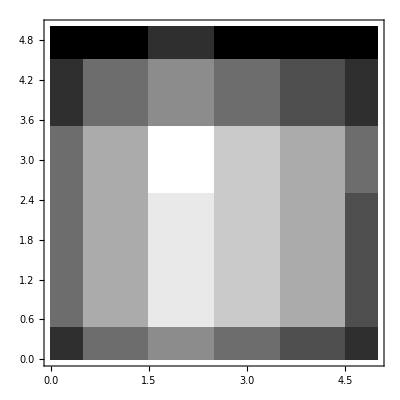

```mathematica
ListContourPlot[ ImageToList[img] , InterpolationOrder->0, ColorFunction->GrayLevel]
```

```mathematica
Reverse[ {{1,2,3} , {4,5,6},{7,8,9}}, 1]
```

(7 | 8 | 9
4 | 5 | 6
1 | 2 | 3)

```mathematica
SubPixel2DGaussianSimpleFit[img_]:= Module[ {data, fit, a,y,x,mx,my,b,s},
data = ImageToList[img] ;
fit =  NonlinearModelFit[data,a Exp@((-(-my+y)^2)/(2 s^2) -(-mx+x)^2/(2 s^2)),{{a,Max@data},{mx,ImageDimensions[img]⟦1⟧/2},{my,ImageDimensions[img]⟦2⟧/2},{s,3}},
{x,y}];
{"pos"->
{mx, my}/.fit["BestFitParameters"]
}
]
```

```mathematica
SubPixel2DGaussianFixedFit[img_]:= Module[ {data, fit, a,y,x,mx,my,b,sx,sy},
data = ImageToList[img] ;
fit =  NonlinearModelFit[data,a Exp@((-(-my+y)^2)/(2 sy^2) -(-mx+x)^2/(2 sx^2)),{{a,Max@data},{mx,ImageDimensions[img]⟦1⟧/2},{my,ImageDimensions[img]⟦2⟧/2},{sx,3},{sy,3}},
{x,y}];
{"pos"->
{mx, my}/.fit["BestFitParameters"]
}
]
```

```mathematica
img = BoundParticleImg[SubstractBG[ GetFrame[ 7 ]], i1,1]
```

-Graphics-

```mathematica
SubPixel2DGaussianSimpleFit[img]
pos/.%
ShowTrackOverlayed[img, %]
```

{pos→{2.37765,1.99031}}

{2.37765,1.99031}

-Graphics-

```mathematica
GetPositions[i1]
```

(66.9615 | 8.65385
78.2 | 7.8)

```mathematica
ComponentMeasurements[i1,"BoundingBox"]
```

{1→{{65.,7.},{69.,11.}},2→{{76.,6.},{80.,10.}}}

```mathematica
ShowTrackOverlayed[img_,list_]:=Show[img,
Graphics@Flatten@{Red,Point[#]&/@list}, 
ImageSize -> Large]
```

```mathematica
FitSubPixel[img_, box_]:= ("pos"/.SubPixel2DGaussianFixedFit[ ImageTrim[ img, box ] ]) + box[[1]]
```

```mathematica
ForFitSubPixel[img_,binImg_, ids_]:=FitSubPixel[img,#]&/@ (ids /. ComponentMeasurements[binImg,"BoundingBox"])
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

(2.00009 | 1341.4)

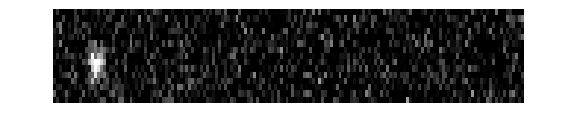

(9.22727 | 12.2273
45.0556 | 8.83333
125.864 | 9.5
62.1667 | 6.61111
48.9 | 3.6
39. | 1.8)

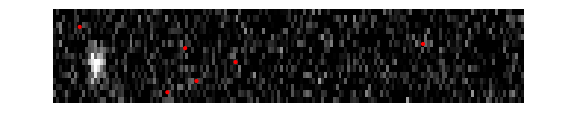

```mathematica
img  = img4;
imgWBG = img4;

ForFitSubPixel[
img, 
FrameBinarize[ imgWBG ], 
{1}]

ShowTrackOverlayed[ img, %]

GetPositions[ FrameBinarize[ imgWBG ]] 
ShowTrackOverlayed[ img, %]
```

### Test Image

```mathematica
dataTest=Round[  255 Table[ Exp[ (- ((16-h)- 6.7)^2)/(2 2^2)-(w-15.3)^2/(2 2^2)], {h,1,15}, {w,1,160}] ];
img4= (Image[dataTest, "Byte"]) ~ ImageEffect ~ {"GaussianNoise",0.2}
```

-Graphics-

```mathematica
ImageToList@-Graphics-
```

```mathematica
GetFrame[ lookAt ] // ImageDimensions
```

{161,15}

```mathematica
SubPixelShow[img_, fns_]:= Show[
Graphics[
Inset[img, {-0.5,-0.5},{Left,Bottom}, img//ImageDimensions]
],

Graphics@Flatten[ 
{RandomColor[],Tooltip[Point[pos/.#@img],#] &/@ fns}
],

ImageSize -> Medium
]
```

```mathematica
SubPixelShow[img, {SubPixel2DGaussianSimpleFit}]
```

-Graphics-

```mathematica
f[x_]:=Module[{},
a = 1;
If[x===1, Return[1]];
3]
```

```mathematica
f[3]
```

3

```mathematica
OptionValue[Plot, 20, 1]
```

OptionValue::rep: 20 is not a valid replacement rule.

OptionValue::optnf: Option name 1 not found in defaults for Plot.

1

```mathematica
Ceiling[1.1]
```

2

```mathematica
from = 1100;
to =  2501;
buffer = 1000;

Ceiling[to,buffer] - Ceiling[from,buffer]< buffer

from
Ceiling[from,buffer]

Min[ Ceiling[from,buffer]+1 , to]
to
```

False

1100

2000

2001

2501

```mathematica
Ceiling[to,buffer]
```

3000

## Lets run the analysis!

```mathematica
i=1;
AnalyseFrame[i]

ShowTrackOverlayed[ GetFrame[i], %]
```

(67.7618 | 8.28603
79.5773 | 9.26234)

-Graphics-

```mathematica
Unzipper[el_]:=If[Length@el[[2]]>0,Map[{el[[1]],#}&,el[[2]]],{}]
```

```mathematica
Unzipper[ {1,{{2,3},{4,5},{6,7}}}]
```

{{1,{2,3}},{1,{4,5}},{1,{6,7}}}

```mathematica
Quit[];
```

```mathematica
<<VideoTracking`

SelectVideo["~/Dropbox/PhD/Software/video-tracking/practice_videos/video_2.avi"]

SelectROI[({{291, 140}, {451, 140}, {451, 126}, {291, 126}})]

UpdateBackgroung[1,NumberOfFrames[]]
```

video_2.avi has 1333 frames and is 720x480

(291 | 140
451 | 140
451 | 126
291 | 126)

-Graphics-

```mathematica
GetFrame[1]
```

-Graphics-

```mathematica
out = RunAnalysis[] // AbsoluteTiming
```

{47.42494,{{1,67.7618,8.28603},{1,79.5773,9.26234},2663,{1333,119.778,7.84597}}}
 |  |  |  |

unparallel execution took ~41.3945 and parallel took 41.389065 

⇒ seems to be diffrent only in initiation 

second time the same:
parallel: 27.24 sec
unparallel 26.8 sec

⇒ keep for now just because might work on better computer

In future need to optimese this by having less globals?

```mathematica
40.3945 sec
```

40.3945 sec

```mathematica
MemoryInUse[] / 1000000 //N
```

112.916

## New buffer testing

```mathematica
<<VideoIO`
```